# Condiciones de regularidad alfa-beta

```mathematica
ff3:=PowerExpand[Simplify[1+(7 r^2 α)/(72 β)-(3 7^(2/3) r^4)/(7 r^6 (7 α^3-324 α β)+36 r^2 β (-216 c β-216 α β+√(-84 r^4 α (c+α) (7 α^2-324 β)-189 r^8 (7 α^2-288 β)+46656 (c+α)^2 β^2)))^(1/3)+(7 7^(2/3) r^4 α^2)/(72 β (7 r^6 (7 α^3-324 α β)+36 r^2 β (-216 c β-216 α β+√(-84 r^4 α (c+α) (7 α^2-324 β)-189 r^8 (7 α^2-288 β)+46656 (c+α)^2 β^2)))^(1/3))+1/(72 β)7^(1/3) (7 r^6 (7 α^3-324 α β)+36 r^2 β (-216 c β-216 α β+√(-84 r^4 α (c+α) (7 α^2-324 β)-189 r^8 (7 α^2-288 β)+46656 (c+α)^2 β^2)))^(1/3)],Assumptions->{α>0,β>0,r>0}]
```

```mathematica
ff3
```

1+(7 r^2 α)/(72 β)-(3 7^(2/3) r^4)/((7 r^6 (7 α^3-324 α β)+36 r^2 β (-216 c β-216 α β+√(-84 r^4 α (c+α) (7 α^2-324 β)-189 r^8 (7 α^2-288 β)+46656 (c+α)^2 β^2)))^(1/3))+(7 7^(2/3) r^4 α^2)/(72 β (7 r^6 (7 α^3-324 α β)+36 r^2 β (-216 c β-216 α β+√(-84 r^4 α (c+α) (7 α^2-324 β)-189 r^8 (7 α^2-288 β)+46656 (c+α)^2 β^2)))^(1/3))+(7^(1/3) (7 r^6 (7 α^3-324 α β)+36 r^2 β (-216 c β-216 α β+√(-84 r^4 α (c+α) (7 α^2-324 β)-189 r^8 (7 α^2-288 β)+46656 (c+α)^2 β^2)))^(1/3))/(72 β)

```mathematica
Simplify[-(3 7^(2/3) r^4)/((7 r^6 (7 α^3-324 α β)+36 r^2 β (-216 c β-216 α β+√(-84 r^4 α (c+α) (7 α^2-324 β)-189 r^8 (7 α^2-288 β)+46656 (c+α)^2 β^2)))^(1/3))+(7 7^(2/3) r^4 α^2)/(72 β (7 r^6 (7 α^3-324 α β)+36 r^2 β (-216 c β-216 α β+√(-84 r^4 α (c+α) (7 α^2-324 β)-189 r^8 (7 α^2-288 β)+46656 (c+α)^2 β^2)))^(1/3))]
```

(7^(2/3) r^4 (7 α^2-216 β))/(72 β (7 r^6 (7 α^3-324 α β)+36 r^2 β (-216 c β-216 α β+√(-84 r^4 α (c+α) (7 α^2-324 β)-189 r^8 (7 α^2-288 β)+46656 (c+α)^2 β^2)))^(1/3))

```mathematica
ff3s=1+(7 r^2 α)/(72 β)+(7^(2/3) r^4 (7 α^2-216 β))/(72 β (7 r^6 (7 α^3-324 α β)+36 r^2 β (-216 c β-216 α β+√(-84 r^4 α (c+α) (7 α^2-324 β)-189 r^8 (7 α^2-288 β)+46656 (c+α)^2 β^2)))^(1/3))+(7^(1/3) (7 r^6 (7 α^3-324 α β)+36 r^2 β (-216 c β-216 α β+√(-84 r^4 α (c+α) (7 α^2-324 β)-189 r^8 (7 α^2-288 β)+46656 (c+α)^2 β^2)))^(1/3))/(72 β)
```

1+(7 r^2 α)/(72 β)+(7^(2/3) r^4 (7 α^2-216 β))/(72 β (7 r^6 (7 α^3-324 α β)+36 r^2 β (-216 c β-216 α β+√(-84 r^4 α (c+α) (7 α^2-324 β)-189 r^8 (7 α^2-288 β)+46656 (c+α)^2 β^2)))^(1/3))+(7^(1/3) (7 r^6 (7 α^3-324 α β)+36 r^2 β (-216 c β-216 α β+√(-84 r^4 α (c+α) (7 α^2-324 β)-189 r^8 (7 α^2-288 β)+46656 (c+α)^2 β^2)))^(1/3))/(72 β)

### Tendencia de f(r) en la región asintótica

```mathematica
FullSimplify[Assuming[α>0&&β>0&&r>0,Simplify[Series[ff3s,{r,Infinity,2}]]]]
```

((7 α+(7^(2/3) (7 α^2-216 β))/((49 α^3-2268 α β+108 √21 β √(-7 α^2+288 β))^(1/3))+7^(1/3) (49 α^3-2268 α β+108 √21 β √(-7 α^2+288 β))^(1/3)) r^2)/(72 β)+1+((c+α) (-2268 α^2 β+93312 β^2+7 √21 α^3 √(-7 α^2+288 β)-324 √21 α β √(-7 α^2+288 β)) (-7 7^(2/3) α^2+216 7^(2/3) β+7^(1/3) (49 α^3-2268 α β+108 √21 β √(-7 α^2+288 β))^(2/3)))/(9 (7 α^2-288 β) (49 α^3-2268 α β+108 √21 β √(-7 α^2+288 β))^(4/3) r^2)+O[1/r]^3

```mathematica
Simplify[Solve[((c+α) (-2268 α^2 β+93312 β^2+7 √21 α^3 √(-7 α^2+288 β)-324 √21 α β √(-7 α^2+288 β)) (-7 7^(2/3) α^2+216 7^(2/3) β+7^(1/3) (49 α^3-2268 α β+108 √21 β √(-7 α^2+288 β))^(2/3)))/(9 (7 α^2-288 β) (49 α^3-2268 α β+108 √21 β √(-7 α^2+288 β))^(4/3))==-μ,c]]
```

{{c→(9 (7 α^2-288 β) (49 α^3-2268 α β+108 √21 β √(-7 α^2+288 β))^(4/3) (-(α (-2268 α^2 β+93312 β^2+7 √21 α^3 √(-7 α^2+288 β)-324 √21 α β √(-7 α^2+288 β)) (-7 7^(2/3) α^2+216 7^(2/3) β+7^(1/3) (49 α^3-2268 α β+108 √21 β √(-7 α^2+288 β))^(2/3)))/(9 (7 α^2-288 β) (49 α^3-2268 α β+108 √21 β √(-7 α^2+288 β))^(4/3))-μ))/((-2268 α^2 β+93312 β^2+7 √21 α^3 √(-7 α^2+288 β)-324 √21 α β √(-7 α^2+288 β)) (-7 7^(2/3) α^2+216 7^(2/3) β+7^(1/3) (49 α^3-2268 α β+108 √21 β √(-7 α^2+288 β))^(2/3)))}}

```mathematica
c:=-μ*(9 (7 α^2-288 β) (49 α^3-2268 α β+108 √21 β √(-7 α^2+288 β))^(4/3))/((-2268 α^2 β+93312 β^2+7 √21 α^3 √(-7 α^2+288 β)-324 √21 α β √(-7 α^2+288 β)) (-7 7^(2/3) α^2+216 7^(2/3) β+7^(1/3) (49 α^3-2268 α β+108 √21 β √(-7 α^2+288 β))^(2/3)))-α
```

```mathematica
FullSimplify[c]
```

-α-(9 (7 α^2-288 β) (49 α^3-2268 α β+108 √21 β √(-7 α^2+288 β))^(4/3) μ)/((-2268 α^2 β+93312 β^2+7 √21 α^3 √(-7 α^2+288 β)-324 √21 α β √(-7 α^2+288 β)) (-7 7^(2/3) α^2+216 7^(2/3) β+7^(1/3) (49 α^3-2268 α β+108 √21 β √(-7 α^2+288 β))^(2/3)))

```mathematica
Assuming[α>0&&β>0&&r>0,Series[ff3s,{r,Infinity,2}]]
```

((7 α)/(72 β)+(7^(2/3) (7 α^2-216 β))/(72 β (49 α^3-2268 α β+108 √21 β √(-7 α^2+288 β))^(1/3))+(7^(1/3) (49 α^3-2268 α β+108 √21 β √(-7 α^2+288 β))^(1/3))/(72 β)) r^2+1-μ/r^2+O[1/r]^3

### Región asintóticamente plana

Less::nord: Invalid comparison with 3.06249-0.972681 ⅈ attempted.

Less::nord: Invalid comparison with 5.36834+4.44089×10^-16 ⅈ attempted.

Less::nord: Invalid comparison with 1.70139-0.739557 ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

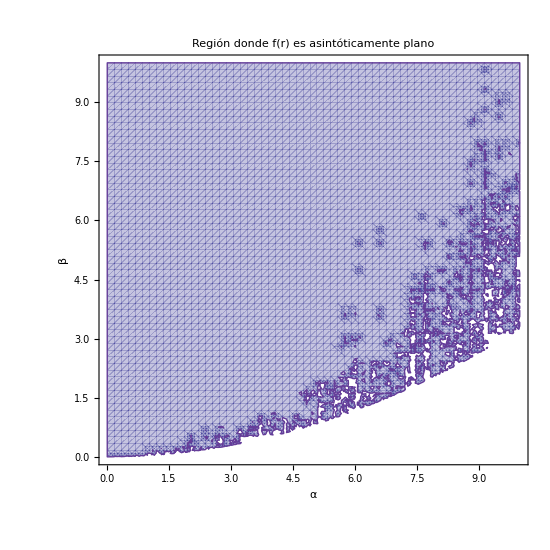

```mathematica
regprim=RegionPlot[(7 7^(2/3) α^2-216 7^(2/3) β+7 α (49 α^3-2268 α β+108 √21 β √(-7 α^2+288 β))^(1/3)+7^(1/3) (49 α^3-2268 α β+108 √21 β √(-7 α^2+288 β))^(2/3))/(72 β (49 α^3-2268 α β+108 √21 β √(-7 α^2+288 β))^(1/3))<(10)^(-29),{α,0,10},{β,0,10},PlotPoints->60,Frame->True,FrameStyle->Directive[Black,1.6],FrameTicksStyle->Directive[Black,14],FrameLabel->{Style["α",20,FontFamily->"Times",Bold],Style["β",20,FontFamily->"Times",Bold]},LabelStyle->Directive[16,FontFamily->"Times"],PlotLabel->Style["Región donde f(r) es asintóticamente plano",22,Bold,FontFamily->"Times"],ImageSize->550,PlotTheme->"Classic",BaseStyle->{FontFamily->"Times",16}]
```

```mathematica
curva=Plot[7*(α^2)/216,{α,0,10},PlotStyle->{Red,Thick}];
curvalit=Plot[108*(α^2)/108,{α,0,10},PlotStyle->{Black,Thick}];
```

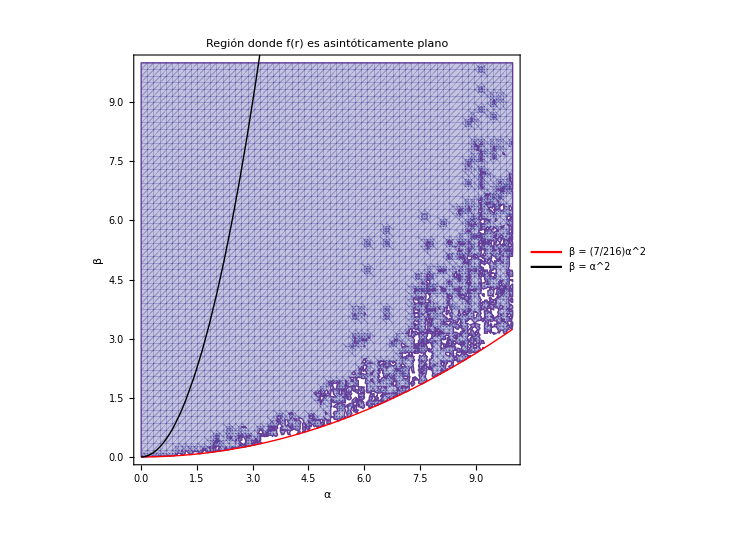

```mathematica
regajus=Legended[Show[regprim,curva,curvalit,PlotRange->{{0,10},{0,10}}],Placed[LineLegend[{Red,Black,Blue,Orange},{Style["β = (7/216)α^2",16,FontFamily->"Times"],Style["β = α^2",16,FontFamily->"Times"]},LegendFunction->Framed,Spacings->1.2],Right]]
```

```mathematica
Export["Restriccion de beta prim para asintitocamente plano.png",regprim]
```

Restriccion de beta prim para asintitocamente plano.png

```mathematica
Export["Restriccion Zprim.png",regajus]
```

Restriccion Zprim.png

### ¿Qué ocurre si β<(7/216) α^2?

```mathematica
fmenor=Assuming[α>0&&r>0,FullSimplify[ff3s/.β->(6/216)α^2]]
```

1/2 (2+(7 r^2)/α+(2^(1/3) 7^(2/3) r^(10/3))/(α (-28 r^4+(9+9 ⅈ √7) α μ+3 √(84 r^8-56 ⅈ (-ⅈ+√7) r^4 α μ+18 ⅈ (3 ⅈ+√7) α^2 μ^2))^(1/3))+(r^(2/3) (-98 r^4+21/2 ((3+3 ⅈ √7) α μ+√(84 r^8-56 ⅈ (-ⅈ+√7) r^4 α μ+18 ⅈ (3 ⅈ+√7) α^2 μ^2)))^(1/3))/α)

La función se vuelve imaginaria

```mathematica
FullSimplify[Assuming[α>0&&β>0&&r>0,Simplify[Series[ff3,{r,Infinity,2}]]]]
```

((7 7^(2/3) α^2-216 7^(2/3) β+7 α (49 α^3-2268 α β+108 √21 β √(-7 α^2+288 β))^(1/3)+7^(1/3) (49 α^3-2268 α β+108 √21 β √(-7 α^2+288 β))^(2/3)) r^2)/(72 β (49 α^3-2268 α β+108 √21 β √(-7 α^2+288 β))^(1/3))+1-μ/r^2+O[1/r]^3

### Región dentro del agujero negro

```mathematica
Clear[c]
```

```mathematica
serieOriginal=Series[ff3,{r,0,2}];
```

```mathematica
Assuming[α>0&&β>0&&r>0&&c>0,FullSimplify[serieOriginal]]
```

1+(7 α r^2)/(72 β)+O[r]^(7/3)

```mathematica
Assuming[α>0&&β>0&&r>0&&μ>0,Simplify[ff3s]]
```

1+(7 r^2 α)/(72 β)+(7^(2/3) r^4 (7 α^2-216 β))/(72 β (7 r^6 (7 α^3-324 α β)+36 r^2 β ((1944 (7 α^2-288 β) β (49 α^3-2268 α β+108 √21 β √(-7 α^2+288 β))^(4/3) μ)/((-2268 α^2 β+93312 β^2+7 √21 α^3 √(-7 α^2+288 β)-324 √21 α β √(-7 α^2+288 β)) (-7 7^(2/3) α^2+216 7^(2/3) β+7^(1/3) (49 α^3-2268 α β+108 √21 β √(-7 α^2+288 β))^(2/3)))+3 √3 √((7 α^2-288 β) (-7 r^8+(4 7^(2/3) r^4 α (7 α^2-324 β) (49 α^3-2268 α β+108 √21 β √(-7 α^2+288 β))^(4/3) μ)/((-2268 α^2 β+93312 β^2+7 √21 α^3 √(-7 α^2+288 β)-324 √21 α β √(-7 α^2+288 β)) (-7 7^(1/3) α^2+216 7^(1/3) β+(49 α^3-2268 α β+108 √21 β √(-7 α^2+288 β))^(2/3)))+(139968 (7 α^2-288 β) β^2 (49 α^3-2268 α β+108 √21 β √(-7 α^2+288 β))^(8/3) μ^2)/((2268 α^2 β-93312 β^2-7 √21 α^3 √(-7 α^2+288 β)+324 √21 α β √(-7 α^2+288 β))^2 (-7 7^(2/3) α^2+216 7^(2/3) β+7^(1/3) (49 α^3-2268 α β+108 √21 β √(-7 α^2+288 β))^(2/3))^2)))))^(1/3))+1/(72 β)7^(1/3) (7 r^6 (7 α^3-324 α β)+36 r^2 β ((1944 (7 α^2-288 β) β (49 α^3-2268 α β+108 √21 β √(-7 α^2+288 β))^(4/3) μ)/((-2268 α^2 β+93312 β^2+7 √21 α^3 √(-7 α^2+288 β)-324 √21 α β √(-7 α^2+288 β)) (-7 7^(2/3) α^2+216 7^(2/3) β+7^(1/3) (49 α^3-2268 α β+108 √21 β √(-7 α^2+288 β))^(2/3)))+3 √3 √((7 α^2-288 β) (-7 r^8+(4 7^(2/3) r^4 α (7 α^2-324 β) (49 α^3-2268 α β+108 √21 β √(-7 α^2+288 β))^(4/3) μ)/((-2268 α^2 β+93312 β^2+7 √21 α^3 √(-7 α^2+288 β)-324 √21 α β √(-7 α^2+288 β)) (-7 7^(1/3) α^2+216 7^(1/3) β+(49 α^3-2268 α β+108 √21 β √(-7 α^2+288 β))^(2/3)))+(139968 (7 α^2-288 β) β^2 (49 α^3-2268 α β+108 √21 β √(-7 α^2+288 β))^(8/3) μ^2)/((2268 α^2 β-93312 β^2-7 √21 α^3 √(-7 α^2+288 β)+324 √21 α β √(-7 α^2+288 β))^2 (-7 7^(2/3) α^2+216 7^(2/3) β+7^(1/3) (49 α^3-2268 α β+108 √21 β √(-7 α^2+288 β))^(2/3))^2)))))^(1/3)

### Reescalado

```mathematica
fsim:=1+(7 r^2 α)/(72 β)+(7^(2/3) r^4 (7 α^2-216 β))/(72 β (7 r^6 (7 α^3-324 α β)+36 r^2 β ((1944 (7 α^2-288 β) β (49 α^3-2268 α β+108 √21 β √(-7 α^2+288 β))^(4/3) μ)/((-2268 α^2 β+93312 β^2+7 √21 α^3 √(-7 α^2+288 β)-324 √21 α β √(-7 α^2+288 β)) (-7 7^(2/3) α^2+216 7^(2/3) β+7^(1/3) (49 α^3-2268 α β+108 √21 β √(-7 α^2+288 β))^(2/3)))+3 √3 √((7 α^2-288 β) (-7 r^8+(4 7^(2/3) r^4 α (7 α^2-324 β) (49 α^3-2268 α β+108 √21 β √(-7 α^2+288 β))^(4/3) μ)/((-2268 α^2 β+93312 β^2+7 √21 α^3 √(-7 α^2+288 β)-324 √21 α β √(-7 α^2+288 β)) (-7 7^(1/3) α^2+216 7^(1/3) β+(49 α^3-2268 α β+108 √21 β √(-7 α^2+288 β))^(2/3)))+(139968 (7 α^2-288 β) β^2 (49 α^3-2268 α β+108 √21 β √(-7 α^2+288 β))^(8/3) μ^2)/((2268 α^2 β-93312 β^2-7 √21 α^3 √(-7 α^2+288 β)+324 √21 α β √(-7 α^2+288 β))^2 (-7 7^(2/3) α^2+216 7^(2/3) β+7^(1/3) (49 α^3-2268 α β+108 √21 β √(-7 α^2+288 β))^(2/3))^2)))))^(1/3))+1/(72 β)7^(1/3) (7 r^6 (7 α^3-324 α β)+36 r^2 β ((1944 (7 α^2-288 β) β (49 α^3-2268 α β+108 √21 β √(-7 α^2+288 β))^(4/3) μ)/((-2268 α^2 β+93312 β^2+7 √21 α^3 √(-7 α^2+288 β)-324 √21 α β √(-7 α^2+288 β)) (-7 7^(2/3) α^2+216 7^(2/3) β+7^(1/3) (49 α^3-2268 α β+108 √21 β √(-7 α^2+288 β))^(2/3)))+3 √3 √((7 α^2-288 β) (-7 r^8+(4 7^(2/3) r^4 α (7 α^2-324 β) (49 α^3-2268 α β+108 √21 β √(-7 α^2+288 β))^(4/3) μ)/((-2268 α^2 β+93312 β^2+7 √21 α^3 √(-7 α^2+288 β)-324 √21 α β √(-7 α^2+288 β)) (-7 7^(1/3) α^2+216 7^(1/3) β+(49 α^3-2268 α β+108 √21 β √(-7 α^2+288 β))^(2/3)))+(139968 (7 α^2-288 β) β^2 (49 α^3-2268 α β+108 √21 β √(-7 α^2+288 β))^(8/3) μ^2)/((2268 α^2 β-93312 β^2-7 √21 α^3 √(-7 α^2+288 β)+324 √21 α β √(-7 α^2+288 β))^2 (-7 7^(2/3) α^2+216 7^(2/3) β+7^(1/3) (49 α^3-2268 α β+108 √21 β √(-7 α^2+288 β))^(2/3))^2)))))^(1/3)
```

```mathematica
FullSimplify[-2268 α^2 β+93312 β^2+7 √21 α^3 √(-7 α^2+288 β)-324 √21 α β √(-7 α^2+288 β)]
```

-2268 α^2 β+93312 β^2+7 √21 α^3 √(-7 α^2+288 β)-324 √21 α β √(-7 α^2+288 β)

Construiremos las siguientes funciones

```mathematica
E1:=-7 α^2+288 β
B1:=49 α^3-2268 α β+108 √21 β √E1
D1:=-2268 α^2 β+93312 β^2+7 √21 α^3 √(-7 α^2+288 β)-324 √21 α β √(-7 α^2+288 β)
D2:=7^(5/3) α^2-7^(1/3) (216 7^(1/3) β+B1^(2/3))
```

```mathematica
C1:=7 r^6 (7 α^3-324 α β)+36 r^2 β (-(1944 (7 α^2-288 β) β (B1)^(4/3) μ)/((D1) (D2))+3 √3 √((7 α^2-288 β) (-7 r^8-(28 r^4 α (7 α^2-324 β) (B1)^(4/3) μ)/((D1) (D2))+(139968 (7 α^2-288 β) β^2 (B1)^(8/3) μ^2)/((D1)^2 (D2)^2))))
```

```mathematica
f3sim=Simplify[1+(7 r^2 α)/(72 β)+(7^(2/3) r^4 (7 α^2-216 β))/(72 β (C1)^(1/3))+1/(72 β)7^(1/3) (C1)^(1/3)]
```

1+(7 r^2 α)/(72 β)+(7^(2/3) r^4 (7 α^2-216 β))/(72 β (7 r^6 (7 α^3-324 α β)+36 r^2 β (-(1944 (7 α^2-288 β) β (49 α^3-2268 α β+108 √21 β √(-7 α^2+288 β))^(4/3) μ)/((-2268 α^2 β+93312 β^2+7 √21 α^3 √(-7 α^2+288 β)-324 √21 α β √(-7 α^2+288 β)) (7 7^(2/3) α^2-7^(1/3) (216 7^(1/3) β+(49 α^3-2268 α β+108 √21 β √(-7 α^2+288 β))^(2/3))))+3 √3 √((7 α^2-288 β) (-7 r^8+(4 7^(2/3) r^4 α (7 α^2-324 β) (49 α^3-2268 α β+108 √21 β √(-7 α^2+288 β))^(4/3) μ)/((-2268 α^2 β+93312 β^2+7 √21 α^3 √(-7 α^2+288 β)-324 √21 α β √(-7 α^2+288 β)) (-7 7^(1/3) α^2+216 7^(1/3) β+(49 α^3-2268 α β+108 √21 β √(-7 α^2+288 β))^(2/3)))+(139968 (7 α^2-288 β) β^2 (49 α^3-2268 α β+108 √21 β √(-7 α^2+288 β))^(8/3) μ^2)/(7^(2/3) (2268 α^2 β-93312 β^2-7 √21 α^3 √(-7 α^2+288 β)+324 √21 α β √(-7 α^2+288 β))^2 (-7 7^(1/3) α^2+216 7^(1/3) β+(49 α^3-2268 α β+108 √21 β √(-7 α^2+288 β))^(2/3))^2)))))^(1/3))+1/(72 β)7^(1/3) (7 r^6 (7 α^3-324 α β)+36 r^2 β (-(1944 (7 α^2-288 β) β (49 α^3-2268 α β+108 √21 β √(-7 α^2+288 β))^(4/3) μ)/((-2268 α^2 β+93312 β^2+7 √21 α^3 √(-7 α^2+288 β)-324 √21 α β √(-7 α^2+288 β)) (7 7^(2/3) α^2-7^(1/3) (216 7^(1/3) β+(49 α^3-2268 α β+108 √21 β √(-7 α^2+288 β))^(2/3))))+3 √3 √((7 α^2-288 β) (-7 r^8+(4 7^(2/3) r^4 α (7 α^2-324 β) (49 α^3-2268 α β+108 √21 β √(-7 α^2+288 β))^(4/3) μ)/((-2268 α^2 β+93312 β^2+7 √21 α^3 √(-7 α^2+288 β)-324 √21 α β √(-7 α^2+288 β)) (-7 7^(1/3) α^2+216 7^(1/3) β+(49 α^3-2268 α β+108 √21 β √(-7 α^2+288 β))^(2/3)))+(139968 (7 α^2-288 β) β^2 (49 α^3-2268 α β+108 √21 β √(-7 α^2+288 β))^(8/3) μ^2)/(7^(2/3) (2268 α^2 β-93312 β^2-7 √21 α^3 √(-7 α^2+288 β)+324 √21 α β √(-7 α^2+288 β))^2 (-7 7^(1/3) α^2+216 7^(1/3) β+(49 α^3-2268 α β+108 √21 β √(-7 α^2+288 β))^(2/3))^2)))))^(1/3)

```mathematica
Assuming[α>0&&β>0&&μ>0&&r>0,Simplify[fsim-f3sim]]
```

0

```mathematica
E1rees=Assuming[α>0&&β>0&&r2>0&&μ>0&&b>0,Simplify[E1/.β->b*α^2/.r->Sqrt[(72 b α)/(7 )]r2]]
B1rees=Assuming[α>0&&β>0&&r2>0&&μ>0&&b>0,Simplify[B1/.β->b*α^2/.r->Sqrt[(72 b α)/(7 )]r2]]
D1rees=Assuming[α>0&&β>0&&r2>0&&μ>0&&b>0,Simplify[D1/.β->b*α^2/.r->Sqrt[(72 b α)/(7 )]r2]]
D2rees=Assuming[α>0&&β>0&&r2>0&&μ>0&&b>0,Simplify[D2/.β->b*α^2/.r->Sqrt[(72 b α)/(7 )]r2]]
C1rees=Assuming[α>0&&β>0&&r2>0&&μ>0&&b>0,Simplify[C1/.β->b*α^2/.r->Sqrt[(72 b α)/(7 )]r2/.μ->72*b*α*μ2/7]]
```

(-7+288 b) α^2

(49+108 b (-21+√21 √(-7+288 b))) α^3

(93312 b^2+7 √21 √(-7+288 b)-324 b (7+√21 √(-7+288 b))) α^4

-7^(1/3) (-7 7^(1/3)+216 7^(1/3) b+(49+108 b (-21+√21 √(-7+288 b)))^(2/3)) α^2

373248/343 b^2 r2^2 α^3 (-7 b (-7+324 b) r2^4 α^3+(972 7^(2/3) b^2 (-7+288 b) (49+108 b (-21+√21 √(-7+288 b)))^(4/3) α^3 μ2)/((-93312 b^2-7 √21 √(-7+288 b)+324 b (7+√21 √(-7+288 b))) (-7 7^(1/3)+216 7^(1/3) b+(49+108 b (-21+√21 √(-7+288 b)))^(2/3)))+18 √42 √((7-288 b) b^3 α^6 (-18 b r2^8+(7^(2/3) (-7+324 b) (49+108 b (-21+√21 √(-7+288 b)))^(4/3) r2^4 μ2)/((-93312 b^2-7 √21 √(-7+288 b)+324 b (7+√21 √(-7+288 b))) (-7 7^(1/3)+216 7^(1/3) b+(49+108 b (-21+√21 √(-7+288 b)))^(2/3)))-(486 7^(1/3) b (-7+288 b) (49+108 b (-21+√21 √(-7+288 b)))^(8/3) μ2^2)/((93312 b^2+7 √21 √(-7+288 b)-324 b (7+√21 √(-7+288 b)))^2 (-7 7^(1/3)+216 7^(1/3) b+(49+108 b (-21+√21 √(-7+288 b)))^(2/3))^2))))

```mathematica
Assuming[b>0&&r2>0&&α>0,Simplify[(373248/343 b^3 r2^2 α^6)^(-1/3)]]
```

7/(72 b r2^(2/3) α^2)

```mathematica
f3rees=Assuming[α>0&&β>0&&r2>0&&μ2>0&&b>0,Simplify[f3sim/.β->b*α^2/.r->Sqrt[(72 b α)/(7 )]r2/.μ->72*b*α*μ2/7]]
```

1+r2^2+(72 (7-216 b) b r2^4 α^2)/(7 (-373248/7 b^3 (-7+324 b) r2^6 α^6+2592 b^2 r2^2 α^3 ((139968 b^2 (-7+288 b) (49+108 b (-21+√21 √(-7+288 b)))^(4/3) α^3 μ2)/(7 7^(1/3) (-93312 b^2-7 √21 √(-7+288 b)+324 b (7+√21 √(-7+288 b))) (-7 7^(1/3)+216 7^(1/3) b+(49+108 b (-21+√21 √(-7+288 b)))^(2/3)))+2592/7 √(6/7) √((7-288 b) b^3 α^6 (-18 b r2^8+(7^(2/3) (-7+324 b) (49+108 b (-21+√21 √(-7+288 b)))^(4/3) r2^4 μ2)/((-93312 b^2-7 √21 √(-7+288 b)+324 b (7+√21 √(-7+288 b))) (-7 7^(1/3)+216 7^(1/3) b+(49+108 b (-21+√21 √(-7+288 b)))^(2/3)))-(486 7^(1/3) b (-7+288 b) (49+108 b (-21+√21 √(-7+288 b)))^(8/3) μ2^2)/((93312 b^2+7 √21 √(-7+288 b)-324 b (7+√21 √(-7+288 b)))^2 (-7 7^(1/3)+216 7^(1/3) b+(49+108 b (-21+√21 √(-7+288 b)))^(2/3))^2)))))^(1/3))+1/(72 b α^2)(-373248/7 b^3 (-7+324 b) r2^6 α^6+2592 b^2 r2^2 α^3 ((139968 b^2 (-7+288 b) (49+108 b (-21+√21 √(-7+288 b)))^(4/3) α^3 μ2)/(7 7^(1/3) (-93312 b^2-7 √21 √(-7+288 b)+324 b (7+√21 √(-7+288 b))) (-7 7^(1/3)+216 7^(1/3) b+(49+108 b (-21+√21 √(-7+288 b)))^(2/3)))+2592/7 √(6/7) √((7-288 b) b^3 α^6 (-18 b r2^8+(7^(2/3) (-7+324 b) (49+108 b (-21+√21 √(-7+288 b)))^(4/3) r2^4 μ2)/((-93312 b^2-7 √21 √(-7+288 b)+324 b (7+√21 √(-7+288 b))) (-7 7^(1/3)+216 7^(1/3) b+(49+108 b (-21+√21 √(-7+288 b)))^(2/3)))-(486 7^(1/3) b (-7+288 b) (49+108 b (-21+√21 √(-7+288 b)))^(8/3) μ2^2)/((93312 b^2+7 √21 √(-7+288 b)-324 b (7+√21 √(-7+288 b)))^2 (-7 7^(1/3)+216 7^(1/3) b+(49+108 b (-21+√21 √(-7+288 b)))^(2/3))^2)))))^(1/3)

```mathematica
f3rees1[r2_,b_,μ2_]:=1+r2^2+((7-216 b) r2^(10/3))/((7^(1/3))*(-7(-7+324 b) r2^4- (972 *(7^(2/3))(-7+288 b) (49+108 b (-21+√21 √(-7+288 b)))^(4/3) b μ2)/((-93312 b^2-7 √21 √(-7+288 b)+324 b (7+√21 √(-7+288 b))) (-7 7^(1/3)+216 7^(1/3) b+(49+108 b (-21+√21 √(-7+288 b)))^(2/3)))+18*(42^(1/2))*√((7-288 b) (-18 (b^2) r2^8+(7^(2/3) (-7+324 b) (49+108 b (-21+√21 √(-7+288 b)))^(4/3)b r2^4 μ2)/((-93312 b^2-7 √21 √(-7+288 b)+324 b (7+√21 √(-7+288 b))) (-7 7^(1/3)+216 7^(1/3) b+(49+108 b (-21+√21 √(-7+288 b)))^(2/3)))-(486 7^(1/3) (b^2) ((-7+288 b)^2) (49+108 b (-21+√21 √(-7+288 b)))^(8/3) μ2^2)/((93312 b^2+7 √21 √(-7+288 b)-324 b (7+√21 √(-7+288 b)))^2 (-7 7^(1/3)+216 7^(1/3) b+(49+108 b (-21+√21 √(-7+288 b)))^(2/3))^2))))^(1/3))+r2^(2/3)/(7^(2/3))(-7(-7+324 b) r2^4- (972 *(7^(2/3))(-7+288 b) (49+108 b (-21+√21 √(-7+288 b)))^(4/3) b μ2)/((93312 b^2+7 √21 √(-7+288 b)-324 b (7+√21 √(-7+288 b))) (-7 7^(1/3)+216 7^(1/3) b+(49+108 b (-21+√21 √(-7+288 b)))^(2/3)))+18*(42^(1/2))*√((7-288 b) (-18 (b^2) r2^8+(7^(2/3) (-7+324 b) (49+108 b (-21+√21 √(-7+288 b)))^(4/3)b r2^4 μ2)/((-93312 b^2-7 √21 √(-7+288 b)+324 b (7+√21 √(-7+288 b))) (-7 7^(1/3)+216 7^(1/3) b+(49+108 b (-21+√21 √(-7+288 b)))^(2/3)))-(486 7^(1/3) (b^2) ((-7+288 b)^2) (49+108 b (-21+√21 √(-7+288 b)))^(8/3) μ2^2)/((93312 b^2+7 √21 √(-7+288 b)-324 b (7+√21 √(-7+288 b)))^2 (-7 7^(1/3)+216 7^(1/3) b+(49+108 b (-21+√21 √(-7+288 b)))^(2/3))^2))))^(1/3)
```

```mathematica
FullSimplify[Assuming[μ>0&&b>0&&r>0,Simplify[Series[f3rees1[r,b,μ],{r,Infinity,2}]]]]
```

(1+(49+108 b (-21+√21 √(-7+288 b)))^(1/3)/7^(2/3)+(7-216 b)/(343+756 b (-21+√21 √(-7+288 b)))^(1/3)) r^2+1-μ/r^2+O[1/r]^(7/3)

```mathematica
FullSimplify[Assuming[μ>0&&b>0&&r>0 ,Simplify[Series[f3rees1[r,b,μ],{r,0,2}]]]]
```

1+1/7^(11/18)(324 b (7^(5/6)+21 √(((-7+288 b)^3 (49+108 b (-21+√21 √(-7+288 b)))^(2/3) (343+216 b (324 b (7+144 b-√21 √(-7+288 b))+7 (-21+√21 √(-7+288 b)))))/((7 √21 √(-7+288 b)+324 b (-7+288 b-√21 √(-7+288 b)))^2 (-7 7^(1/3)+216 7^(1/3) b+(49+108 b (-21+√21 √(-7+288 b)))^(2/3))^2))) μ+1/(2 (-7+216 b))3 7^(1/6) (7 7^(1/3) (49+108 b (-21+√21 √(-7+288 b)))^(2/3)+49 (7^(2/3)+(49+108 b (-21+√21 √(-7+288 b)))^(1/3))-108 b (14 7^(2/3)+21 (49+108 b (-21+√21 √(-7+288 b)))^(1/3)+√21 √(-7+288 b) (49+108 b (-21+√21 √(-7+288 b)))^(1/3)+2 7^(1/3) (49+108 b (-21+√21 √(-7+288 b)))^(2/3))) μ)^(1/3) r^(2/3)+r^2+O[r]^(8/3)

### Extremal Black Hole

Intentaremos buscar el extremal Black Hole para b=1. Existe raíz para μ>0.05. Esto debido a que los españoles estudian una torre infinita con este tipo de acoplamiento. En realidad α puede ser cualquier valor pero es necesario estudiar un caso concreto para poder resolver el sistema.

```mathematica
f=FullSimplify[f3rees1[r,1,μ]]
```

1+r^2-(209 r^(10/3))/(7^(1/3) (-2219 r^4-2268 μ+18 √14 √(15174 r^8+2219 r^4 μ+318654 μ^2))^(1/3))+(r^(2/3) (-2219 r^4-2268 μ+18 √14 √(15174 r^8+2219 r^4 μ+318654 μ^2))^(1/3))/7^(2/3)

```mathematica
df=Simplify[D[f3rees1[r2,1,0.03,μ],r2]]
```

2 r2+(0.644914 r2^4 (-0.0739329 r2^5+(0.0217175 r2^5 (36 r2^4-(317 7^(2/3) (-2219+108 √5901)^(4/3) μ)/((-91044+317 √5901) (209 7^(1/3)+(-2219+108 √5901)^(2/3)))))/(√(18 r2^8-(317 7^(2/3) (-2219+108 √5901)^(4/3) r2^4 μ)/((-91044+317 √5901) (209 7^(1/3)+(-2219+108 √5901)^(2/3)))+(136566 7^(1/3) (-2219+108 √5901)^(8/3) μ^2)/((91044-317 √5901)^2 (209 7^(1/3)+(-2219+108 √5901)^(2/3))^2)))+0.139968 r2 (-0.179959 μ+0.15516 √(18 r2^8-(317 7^(2/3) (-2219+108 √5901)^(4/3) r2^4 μ)/((-91044+317 √5901) (209 7^(1/3)+(-2219+108 √5901)^(2/3)))+(136566 7^(1/3) (-2219+108 √5901)^(8/3) μ^2)/((91044-317 √5901)^2 (209 7^(1/3)+(-2219+108 √5901)^(2/3))^2)))))/(-0.0123221 r2^6+0.069984 r2^2 (-0.179959 μ+0.15516 √(18 r2^8-(317 7^(2/3) (-2219+108 √5901)^(4/3) r2^4 μ)/((-91044+317 √5901) (209 7^(1/3)+(-2219+108 √5901)^(2/3)))+(136566 7^(1/3) (-2219+108 √5901)^(8/3) μ^2)/((91044-317 √5901)^2 (209 7^(1/3)+(-2219+108 √5901)^(2/3))^2))))^(4/3)+(5.14403 (-0.0739329 r2^5+(0.0217175 r2^5 (36 r2^4-(317 7^(2/3) (-2219+108 √5901)^(4/3) μ)/((-91044+317 √5901) (209 7^(1/3)+(-2219+108 √5901)^(2/3)))))/(√(18 r2^8-(317 7^(2/3) (-2219+108 √5901)^(4/3) r2^4 μ)/((-91044+317 √5901) (209 7^(1/3)+(-2219+108 √5901)^(2/3)))+(136566 7^(1/3) (-2219+108 √5901)^(8/3) μ^2)/((91044-317 √5901)^2 (209 7^(1/3)+(-2219+108 √5901)^(2/3))^2)))+0.139968 r2 (-0.179959 μ+0.15516 √(18 r2^8-(317 7^(2/3) (-2219+108 √5901)^(4/3) r2^4 μ)/((-91044+317 √5901) (209 7^(1/3)+(-2219+108 √5901)^(2/3)))+(136566 7^(1/3) (-2219+108 √5901)^(8/3) μ^2)/((91044-317 √5901)^2 (209 7^(1/3)+(-2219+108 √5901)^(2/3))^2)))))/(-0.0123221 r2^6+0.069984 r2^2 (-0.179959 μ+0.15516 √(18 r2^8-(317 7^(2/3) (-2219+108 √5901)^(4/3) r2^4 μ)/((-91044+317 √5901) (209 7^(1/3)+(-2219+108 √5901)^(2/3)))+(136566 7^(1/3) (-2219+108 √5901)^(8/3) μ^2)/((91044-317 √5901)^2 (209 7^(1/3)+(-2219+108 √5901)^(2/3))^2))))^(2/3)-(7.73897 r2^3)/((-0.0123221 r2^6+0.069984 r2^2 (-0.179959 μ+0.15516 √(18 r2^8-(317 7^(2/3) (-2219+108 √5901)^(4/3) r2^4 μ)/((-91044+317 √5901) (209 7^(1/3)+(-2219+108 √5901)^(2/3)))+(136566 7^(1/3) (-2219+108 √5901)^(8/3) μ^2)/((91044-317 √5901)^2 (209 7^(1/3)+(-2219+108 √5901)^(2/3))^2))))^(1/3))

```mathematica
sol=NSolve[{f==0,df==0,r2>0,μ>0},{r2,μ},Reals]
```

$Aborted

### Casos fuera del constraint

Un caso especial b=1/16

```mathematica
b:=1/16
α:=0.5
Simplify[E1rees]
Simplify[B1rees]
Simplify[D1rees]
Simplify[D2rees]
Simplify[C1rees]
Clear[b,α]
```

0.5

-0.000312518

-0.000204591

0.233111-0.00762922 ⅈ

-0.0113507 r2^2 (1. r2^4-(1.44+2.69399 ⅈ) μ2-1.8854 √(0.28125 r2^8-(0.810185+1.51572 ⅈ) r2^4 μ2-(1.45833-2.18263 ⅈ) μ2^2))

Un caso interesante b=7/288. Es un caso trivial ya que la función no depende de μ

Otro caso, bueno para analizar es b=7/324

```mathematica
b:=7/324
Simplify[E1rees]
Simplify[B1rees]
Simplify[D1rees]
Assuming[α>0&&r2>0,FullSimplify[D2rees]]
Simplify[C1rees]
Assuming[α>0&&r2>0,FullSimplify[f3rees]]
Clear[b,α]
```

-(7 α^2)/9

(49 ⅈ α^3)/(3 √3)

-(49 α^4)/9

-7/3 (-7)^(2/3) α^2

(392 r2^2 α^3 (-9 α^3 μ2+√3 √(-α^6 (r2^8-27 μ2^2))))/6561

1+r2^2+r2^(10/3)/(√3 (-3 √3 μ2+√(-r2^8+27 μ2^2))^(1/3))+(r2^(2/3) (-3 √3 μ2+√(-r2^8+27 μ2^2))^(1/3))/(√3)

```mathematica
Assuming[μ2>0&&r2>0,FullSimplify[Series[1+r2^2+r2^(10/3)/(√3 (-3 √3 μ2+√(-r2^8+27 μ2^2))^(1/3))+(r2^(2/3) (-3 √3 μ2+√(-r2^8+27 μ2^2))^(1/3))/(√3),{r2,Infinity,2}]]]
```

2 r2^2+1-μ2/r2^2+O[1/r2]^(7/3)

```mathematica
Assuming[μ2>0&&r2>0,FullSimplify[Series[1+r2^2+r2^(10/3)/(√3 (-3 √3 μ2+√(-r2^8+27 μ2^2))^(1/3))+(r2^(2/3) (-3 √3 μ2+√(-r2^8+27 μ2^2))^(1/3))/(√3),{r2,0,2}]]]
```

1+μ2^(1/3)  r2^(2/3)+r2^2+O[r2]^(7/3)

Power::infy: Infinite expression 1/0.^(1/3) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

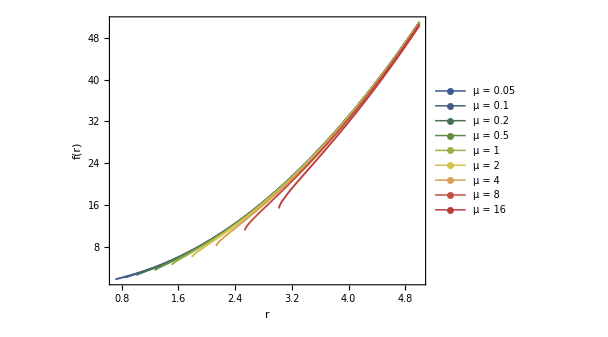

```mathematica
ClearAll[α,b];

b:=7/324;

muVals={0.05,0.1,0.2,0.5,1,2,4,8,16};

paperPlot=Plot[Evaluate@Table[1+r2^2+r2^(10/3)/(√3 (-3 √3 μ2+√(-r2^8+27 μ2^2))^(1/3))+(r2^(2/3) (-3 √3 μ2+√(-r2^8+27 μ2^2))^(1/3))/(√3),{μ2,muVals}],{r2,0,5},(*Estilo general*)PlotRange->All,MaxRecursion->6,ImageSize->450,AspectRatio->0.75,(*Líneas*)PlotStyle->Table[{Thickness[0.003],ColorData["DarkRainbow"][i]},{i,0,1,1/(Length[muVals]-1)}],(*Marco tipo paper*)Frame->True,Axes->False,FrameStyle->Directive[Black,Thickness[0.002]],(*Etiquetas*)FrameLabel->{Style["r",18,FontFamily->"Times"],Style["f(r)",18,FontFamily->"Times"]},(*Ticks*)FrameTicksStyle->Directive[14,FontFamily->"Times"],(*Leyenda*)PlotLegends->Placed[LineLegend[Table[Style[Row[{"μ = ",mu}],14,FontFamily->"Times"],{mu,muVals}],LegendMarkers->"",Spacings->0.8],Right]];

paperPlot

Clear[α,b];
```

```mathematica
Export["Casob7324.png",paperPlot]
```

Casob7324.png

### Expansión de la función reescalada y Constraint

```mathematica
Assuming[α>0&&μ2>0&&b>0&&r2>0,Simplify[Series[f3rees,{r2,Infinity,2}]]]
```

(1+(7-108 b)/(7^(1/3) (49+54 b (-21+√21 √(-7+144 b)))^(1/3))+(49+54 b (-21+√21 √(-7+144 b)))^(1/3)/7^(2/3)) r2^2+1-μ2/r2^2+O[1/r2]^(7/3)

```mathematica
Assuming[α>0&&μ2>0&&b>0&&r2>0,Simplify[Series[f3rees,{r2,0,2}]]]
```

1+1/2^(1/3)3 ((((1944 b^2 (4 √3 7^(1/6) (49+54 b (-21+√21 √(-7+144 b)))^(1/3)+63 √3 √(((-7+144 b) (49+54 b (-21+√21 √(-7+144 b)))^(2/3) (343+1259712 b^3+756 b (-21+√21 √(-7+144 b))-17496 b^2 (-7+√21 √(-7+144 b))))/((7 √21-162 b (√21-√(-7+144 b)))^2 (-7 7^(1/3)+108 7^(1/3) b+(49+54 b (-21+√21 √(-7+144 b)))^(2/3))^2))-9 √7 √(-7+144 b) √(((-7+144 b) (49+54 b (-21+√21 √(-7+144 b)))^(2/3) (343+1259712 b^3+756 b (-21+√21 √(-7+144 b))-17496 b^2 (-7+√21 √(-7+144 b))))/((7 √21-162 b (√21-√(-7+144 b)))^2 (-7 7^(1/3)+108 7^(1/3) b+(49+54 b (-21+√21 √(-7+144 b)))^(2/3))^2)))+7 (7^(2/3) √(-7+144 b) (49+54 b (-21+√21 √(-7+144 b)))^(1/3)+49 √3 √(((-7+144 b) (49+54 b (-21+√21 √(-7+144 b)))^(2/3) (343+1259712 b^3+756 b (-21+√21 √(-7+144 b))-17496 b^2 (-7+√21 √(-7+144 b))))/((7 √21-162 b (√21-√(-7+144 b)))^2 (-7 7^(1/3)+108 7^(1/3) b+(49+54 b (-21+√21 √(-7+144 b)))^(2/3))^2))-√3 7^(2/3) (49+54 b (-21+√21 √(-7+144 b)))^(2/3) √(((-7+144 b) (49+54 b (-21+√21 √(-7+144 b)))^(2/3) (343+1259712 b^3+756 b (-21+√21 √(-7+144 b))-17496 b^2 (-7+√21 √(-7+144 b))))/((7 √21-162 b (√21-√(-7+144 b)))^2 (-7 7^(1/3)+108 7^(1/3) b+(49+54 b (-21+√21 √(-7+144 b)))^(2/3))^2)))+54 b (-7 √3 7^(1/6) (49+54 b (-21+√21 √(-7+144 b)))^(1/3)-3 7^(2/3) √(-7+144 b) (49+54 b (-21+√21 √(-7+144 b)))^(1/3)-245 √3 √(((-7+144 b) (49+54 b (-21+√21 √(-7+144 b)))^(2/3) (343+1259712 b^3+756 b (-21+√21 √(-7+144 b))-17496 b^2 (-7+√21 √(-7+144 b))))/((7 √21-162 b (√21-√(-7+144 b)))^2 (-7 7^(1/3)+108 7^(1/3) b+(49+54 b (-21+√21 √(-7+144 b)))^(2/3))^2))+21 √7 √(-7+144 b) √(((-7+144 b) (49+54 b (-21+√21 √(-7+144 b)))^(2/3) (343+1259712 b^3+756 b (-21+√21 √(-7+144 b))-17496 b^2 (-7+√21 √(-7+144 b))))/((7 √21-162 b (√21-√(-7+144 b)))^2 (-7 7^(1/3)+108 7^(1/3) b+(49+54 b (-21+√21 √(-7+144 b)))^(2/3))^2))+3 √3 7^(2/3) (49+54 b (-21+√21 √(-7+144 b)))^(2/3) √(((-7+144 b) (49+54 b (-21+√21 √(-7+144 b)))^(2/3) (343+1259712 b^3+756 b (-21+√21 √(-7+144 b))-17496 b^2 (-7+√21 √(-7+144 b))))/((7 √21-162 b (√21-√(-7+144 b)))^2 (-7 7^(1/3)+108 7^(1/3) b+(49+54 b (-21+√21 √(-7+144 b)))^(2/3))^2))-3 7^(1/6) √(-7+144 b) (49+54 b (-21+√21 √(-7+144 b)))^(2/3) √(((-7+144 b) (49+54 b (-21+√21 √(-7+144 b)))^(2/3) (343+1259712 b^3+756 b (-21+√21 √(-7+144 b))-17496 b^2 (-7+√21 √(-7+144 b))))/((7 √21-162 b (√21-√(-7+144 b)))^2 (-7 7^(1/3)+108 7^(1/3) b+(49+54 b (-21+√21 √(-7+144 b)))^(2/3))^2)))) μ)/((-7 √21+162 b (√21-√(-7+144 b))) (-7 7^(1/3)+108 7^(1/3) b+(49+54 b (-21+√21 √(-7+144 b)))^(2/3)) α)))^(1/3) r2^(2/3)+r2^2+O[r2]^(7/3)

```mathematica
Solve[1+(49+108 b (-21+√21 √(-7+288 b)))^(1/3)/7^(2/3)+(7-216 b)/(343+756 b (-21+√21 √(-7+288 b)))^(1/3)==0,b]
```

{{}}

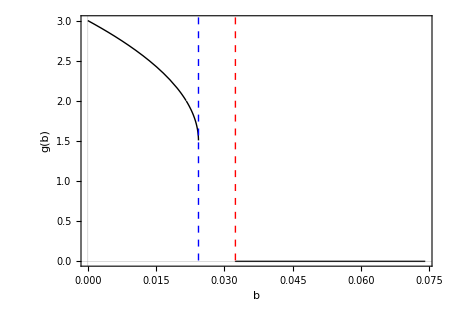

```mathematica
figb1=Plot[1+(49+108 b (-21+√21 √(-7+288 b)))^(1/3)/7^(2/3)+(7-216 b)/(343+756 b (-21+√21 √(-7+288 b)))^(1/3),{b,0,8/108},PlotRange->All,PlotStyle->{Black,Thick},Frame->True,Axes->False,FrameLabel->{Style["b",16,FontFamily->"Times"],Style["g(b)",16,FontFamily->"Times"]},FrameTicks->{Automatic,Automatic},LabelStyle->Directive[14,FontFamily->"Times"],ImageSize->450,AspectRatio->0.7,PlotTheme->"Scientific",Epilog->{{Red,Dashed,Thick,InfiniteLine[{{7/216,0},{7/216,1}}]},Text[Style["b = 7/216",14,Red,FontFamily->"Times"],{-1,0}],{Blue,Dashed,Thick,InfiniteLine[{{7/288,0},{7/288,1}}]},Text[Style["b = 7/288",14,Blue,FontFamily->"Times"],{-1,0}]}]
```

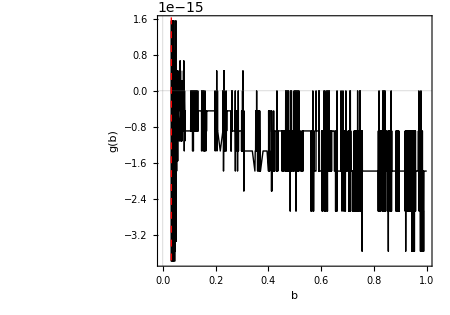

```mathematica
figb2=Plot[1+(49+108 b (-21+√21 √(-7+288 b)))^(1/3)/7^(2/3)+(7-216 b)/(343+756 b (-21+√21 √(-7+288 b)))^(1/3),{b,1/216,1},PlotRange->Automatic,PlotStyle->{Black,Thick},Frame->True,Axes->False,FrameLabel->{Style["b",16,FontFamily->"Times"],Style["g(b)",16,FontFamily->"Times"]},FrameTicks->{Automatic,Automatic},LabelStyle->Directive[14,FontFamily->"Times"],ImageSize->450,AspectRatio->0.7,PlotTheme->"Scientific",Epilog->{{Red,Dashed,Thick,InfiniteLine[{{7/216,0},{7/216,1}}]},Text[Style["b = 7/216",14,Red,FontFamily->"Times"],{-1,0}]}]
```

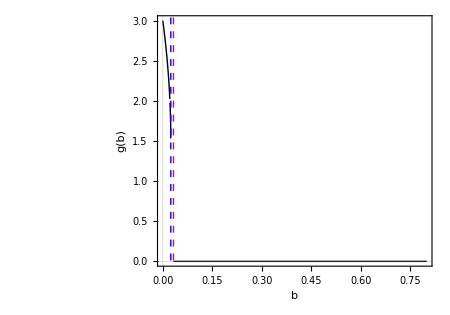

```mathematica
figb3=Plot[1+(49+108 b (-21+√21 √(-7+288 b)))^(1/3)/7^(2/3)+(7-216 b)/(343+756 b (-21+√21 √(-7+288 b)))^(1/3),{b,0,0.8},PlotRange->All,PlotStyle->{Black,Thick},Frame->True,Axes->False,FrameLabel->{Style["b",16,FontFamily->"Times"],Style["g(b)",16,FontFamily->"Times"]},LabelStyle->Directive[14,FontFamily->"Times"],ImageSize->450,AspectRatio->0.7,PlotTheme->"Scientific",Epilog->{{Red,Dashed,Thick,InfiniteLine[{{7/216,0},{7/216,1}}]},Text[Style["b = 7/216",14,Red,FontFamily->"Times"],{-1,0}],{Blue,Dashed,Thick,InfiniteLine[{{7/288,0},{7/288,1}}]},Text[Style["b = 7/288",14,Blue,FontFamily->"Times"],{-1,0}]}]
```

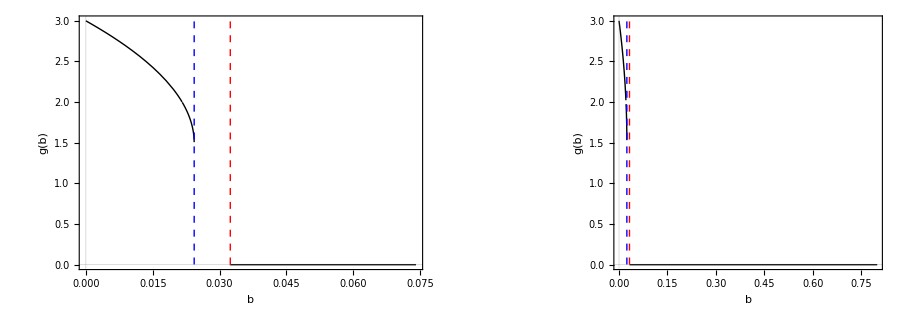

```mathematica
figb=GraphicsRow[{figb1,figb3},ImageSize->900,Spacings->20]
```

```mathematica
Export["Constraint b Zprim.png",figb]
```

Constraint b Zprim.png

### Otro reescalado β=l^2 α

```mathematica
f3rees2=Assuming[α>0&&β>0&&r2>0&&μ>0&&l>0,Simplify[f3sim/.β->l^2*α/.r->Sqrt[36/7]l*r2]]
```

1+r2^2+(36 l^2 r2^4 (-108 l^2+7 α))/(7 (-46656/7 l^6 r2^6 (162 l^2-7 α) α^2+(629856 l^6 r2^2 α^2 √((144 l^2-7 α) α) (49 α^3+54 l^2 α (-21 α+√21 √((144 l^2-7 α) α)))^(4/3) μ)/((7 √21 α^3+162 l^2 α (-√21 α+√((144 l^2-7 α) α))) (-108 7^(2/3) l^2 α+7 7^(2/3) α^2-7^(1/3) (49 α^3+54 l^2 α (-21 α+√21 √((144 l^2-7 α) α)))^(2/3)))+69984/7 l^6 r2^2 α √(3888/7 l^4 r2^8 (144 l^2-7 α) α-(84 r2^4 α^2 √((144 l^2-7 α) α) (-162 l^2+7 α) (49 α^3+54 l^2 α (-21 α+√21 √((144 l^2-7 α) α)))^(4/3) μ)/((7 √21 α^3+162 l^2 α (-√21 α+√((144 l^2-7 α) α))) (108 7^(2/3) l^2 α-7 7^(2/3) α^2+7^(1/3) (49 α^3+54 l^2 α (-21 α+√21 √((144 l^2-7 α) α)))^(2/3)))+(3969 (144 l^2-7 α) α^3 (49 α^3+54 l^2 α (-21 α+√21 √((144 l^2-7 α) α)))^(8/3) μ^2)/((7 √21 α^3+162 l^2 α (-√21 α+√((144 l^2-7 α) α)))^2 (108 7^(2/3) l^2 α-7 7^(2/3) α^2+7^(1/3) (49 α^3+54 l^2 α (-21 α+√21 √((144 l^2-7 α) α)))^(2/3))^2)))^(1/3))+1/(36 l^2 α)(-46656/7 l^6 r2^6 (162 l^2-7 α) α^2+(629856 l^6 r2^2 α^2 √((144 l^2-7 α) α) (49 α^3+54 l^2 α (-21 α+√21 √((144 l^2-7 α) α)))^(4/3) μ)/((7 √21 α^3+162 l^2 α (-√21 α+√((144 l^2-7 α) α))) (-108 7^(2/3) l^2 α+7 7^(2/3) α^2-7^(1/3) (49 α^3+54 l^2 α (-21 α+√21 √((144 l^2-7 α) α)))^(2/3)))+69984/7 l^6 r2^2 α √(3888/7 l^4 r2^8 (144 l^2-7 α) α-(84 r2^4 α^2 √((144 l^2-7 α) α) (-162 l^2+7 α) (49 α^3+54 l^2 α (-21 α+√21 √((144 l^2-7 α) α)))^(4/3) μ)/((7 √21 α^3+162 l^2 α (-√21 α+√((144 l^2-7 α) α))) (108 7^(2/3) l^2 α-7 7^(2/3) α^2+7^(1/3) (49 α^3+54 l^2 α (-21 α+√21 √((144 l^2-7 α) α)))^(2/3)))+(3969 (144 l^2-7 α) α^3 (49 α^3+54 l^2 α (-21 α+√21 √((144 l^2-7 α) α)))^(8/3) μ^2)/((7 √21 α^3+162 l^2 α (-√21 α+√((144 l^2-7 α) α)))^2 (108 7^(2/3) l^2 α-7 7^(2/3) α^2+7^(1/3) (49 α^3+54 l^2 α (-21 α+√21 √((144 l^2-7 α) α)))^(2/3))^2)))^(1/3)

```mathematica
E1rees2=Assuming[α>0&&β>0&&r2>0&&μ>0&&b>0,Simplify[E1/.β->l^2*α/.r->Sqrt[36/7]l*r2]]
B1rees2=Assuming[α>0&&β>0&&r2>0&&μ>0&&b>0,Simplify[B1/.β->l^2*α/.r->Sqrt[36/7]l*r2]]
D1rees2=Assuming[α>0&&β>0&&r2>0&&μ>0&&b>0,Simplify[D1/.β->l^2*α/.r->Sqrt[36/7]l*r2]]
D2rees2=Assuming[α>0&&β>0&&r2>0&&μ>0&&b>0,Simplify[D2/.β->l^2*α/.r->Sqrt[36/7]l*r2]]
C1rees2=Assuming[α>0&&β>0&&r2>0&&μ>0&&b>0,Simplify[C1/.β->l^2*α/.r->Sqrt[36/7]l*r2]]
```

(144 l^2-7 α) α

49 α^3+54 l^2 α (-21 α+√21 √((144 l^2-7 α) α))

7 √21 α^3+162 l^2 α (-√21 α+√((144 l^2-7 α) α))

-108 7^(2/3) l^2 α+7 7^(2/3) α^2-7^(1/3) (49 α^3+54 l^2 α (-21 α+√21 √((144 l^2-7 α) α)))^(2/3)

-46656/49 l^6 r2^6 (162 l^2-7 α) α^2+(629856 l^6 r2^2 α^2 √((144 l^2-7 α) α) (49 α^3+54 l^2 α (-21 α+√21 √((144 l^2-7 α) α)))^(4/3) μ)/(7 (7 √21 α^3+162 l^2 α (-√21 α+√((144 l^2-7 α) α))) (-108 7^(2/3) l^2 α+7 7^(2/3) α^2-7^(1/3) (49 α^3+54 l^2 α (-21 α+√21 √((144 l^2-7 α) α)))^(2/3)))+69984/49 √(3/7) l^4 r2^2 α √(l^4 (1296 l^4 r2^8 (144 l^2-7 α) α-(196 r2^4 α^2 √((144 l^2-7 α) α) (-162 l^2+7 α) (49 α^3+54 l^2 α (-21 α+√21 √((144 l^2-7 α) α)))^(4/3) μ)/((7 √21 α^3+162 l^2 α (-√21 α+√((144 l^2-7 α) α))) (108 7^(2/3) l^2 α-7 7^(2/3) α^2+7^(1/3) (49 α^3+54 l^2 α (-21 α+√21 √((144 l^2-7 α) α)))^(2/3)))+(9261 (144 l^2-7 α) α^3 (49 α^3+54 l^2 α (-21 α+√21 √((144 l^2-7 α) α)))^(8/3) μ^2)/((7 √21 α^3+162 l^2 α (-√21 α+√((144 l^2-7 α) α)))^2 (108 7^(2/3) l^2 α-7 7^(2/3) α^2+7^(1/3) (49 α^3+54 l^2 α (-21 α+√21 √((144 l^2-7 α) α)))^(2/3))^2)))

### Casos dentro del constraint

Variamos α y b

#### α=0.005 y b=8/108

1+r2^2-(9.52381×10^-6 r2^4)/((-2.1164×10^-13 r2^6-2.66667×10^-10 r2^2 μ+1.79583×10^-10 r2^2 √(1.39683×10^-6 r2^8+0.0035 r2^4 μ+2.205 μ^2))^(1/3))+15000. (-2.1164×10^-13 r2^6-2.66667×10^-10 r2^2 μ+1.79583×10^-10 r2^2 √(1.39683×10^-6 r2^8+0.0035 r2^4 μ+2.205 μ^2))^(1/3)

Power::infy: Infinite expression 1/0.^(1/3) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

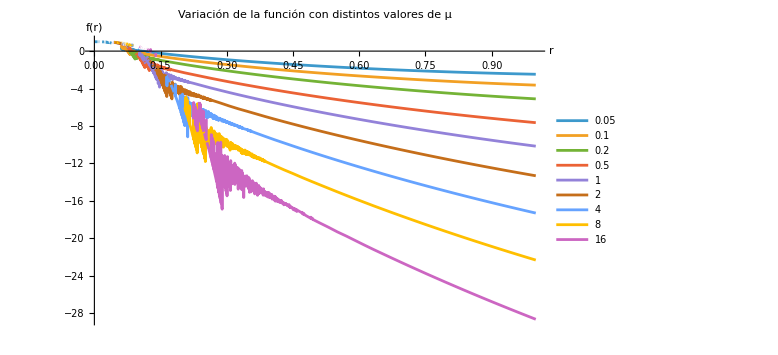

```mathematica
α:=0.005
b:=8/108
f3rees
Plot[Evaluate@Table[f3rees,{μ,{0.05,0.1,0.2,0.5,1,2,4,8,16}}],{r2,0,1},PlotRange->All,MaxRecursion->6,PlotLegends->Placed[{"0.05","0.1","0.2","0.5","1","2","4","8","16"},Right],PlotLabel->"Variación de la función con distintos valores de μ",AxesLabel->{Style["r",18,Bold],Style["f(r)",18,Bold],Style["f(r)",18,Bold]},LabelStyle->Directive[15],TicksStyle->Directive[14],ImageSize->Large]
Clear[α,b]
```

#### α=0.005 y b=1/16

1+r^2+1/7^(2/3)r^(2/3) (-2219 r^4-(273132 7^(2/3) (49+108 (-21+√5901))^(4/3) μ)/((93312+7 √5901-324 (7+√5901)) (209 7^(1/3)+(49+108 (-21+√5901))^(2/3)))+18 √11802 √(18 r^8-(317 7^(2/3) (49+108 (-21+√5901))^(4/3) r^4 μ)/((-93312-7 √5901+324 (7+√5901)) (209 7^(1/3)+(49+108 (-21+√5901))^(2/3)))+(38375046 7^(1/3) (49+108 (-21+√5901))^(8/3) μ^2)/((93312+7 √5901-324 (7+√5901))^2 (209 7^(1/3)+(49+108 (-21+√5901))^(2/3))^2)))^(1/3)-(209 r^(10/3))/(7^(1/3) (-2219 r^4-(273132 7^(2/3) (49+108 (-21+√5901))^(4/3) μ)/((-93312-7 √5901+324 (7+√5901)) (209 7^(1/3)+(49+108 (-21+√5901))^(2/3)))+18 √11802 √(18 r^8-(317 7^(2/3) (49+108 (-21+√5901))^(4/3) r^4 μ)/((-93312-7 √5901+324 (7+√5901)) (209 7^(1/3)+(49+108 (-21+√5901))^(2/3)))+(38375046 7^(1/3) (49+108 (-21+√5901))^(8/3) μ^2)/((93312+7 √5901-324 (7+√5901))^2 (209 7^(1/3)+(49+108 (-21+√5901))^(2/3))^2)))^(1/3))

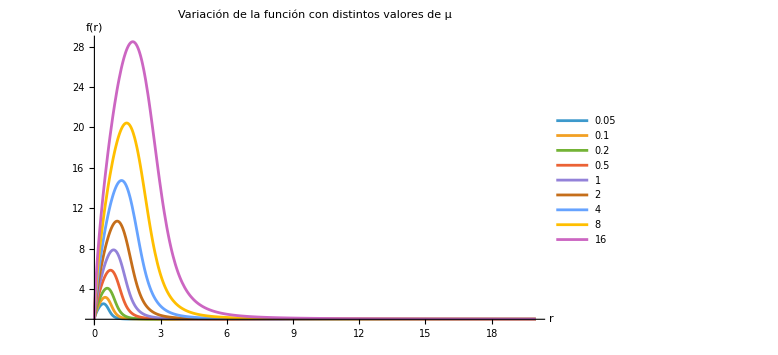

```mathematica
α:=0.0005
b:=1
f3rees1[r,b,μ]
Plot[Evaluate@Table[f3rees1[r,b,μ],{μ,{0.05,0.1,0.2,0.5,1,2,4,8,16}}],{r,0,20},PlotRange->All,MaxRecursion->6,PlotLegends->Placed[{"0.05","0.1","0.2","0.5","1","2","4","8","16"},Right],PlotLabel->"Variación de la función con distintos valores de μ",AxesLabel->{Style["r",18,Bold],Style["f(r)",18,Bold],Style["f(r)",18,Bold]},LabelStyle->Directive[15],TicksStyle->Directive[14],ImageSize->Large]
Clear[α,b]
```

#### α=0.005 y b=1/2

f3rees

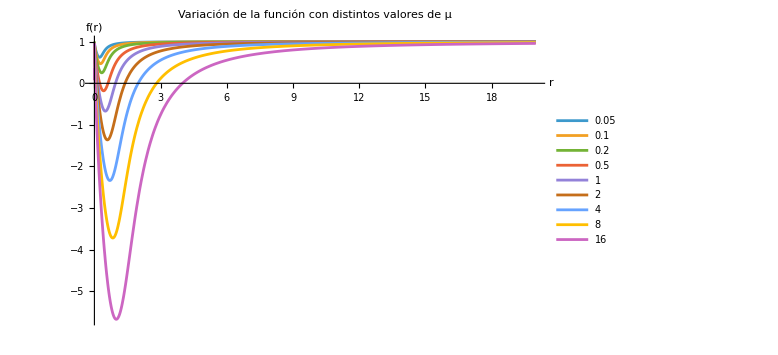

```mathematica
α:=0.005
b:=1/2
f3rees
Plot[Evaluate@Table[f3rees1[r2,b,α,μ],{μ,{0.05,0.1,0.2,0.5,1,2,4,8,16}}],{r2,0,20},PlotRange->All,MaxRecursion->6,PlotLegends->Placed[{"0.05","0.1","0.2","0.5","1","2","4","8","16"},Right],PlotLabel->"Variación de la función con distintos valores de μ",AxesLabel->{Style["r",18,Bold],Style["f(r)",18,Bold],Style["f(r)",18,Bold]},LabelStyle->Directive[15],TicksStyle->Directive[14],ImageSize->Large]
Clear[α,b]
```

#### α=0.03 y b=1

```mathematica
f3rees1[r,1,0.03,μ]
```

1+r^2+1/7^(2/3)r^(2/3) (-1085 r^4+(486 7^(2/3) √137 (49+54 (-21+√2877))^(4/3) μ)/((-7 √21+162 (√21-√137)) (101 7^(1/3)+(49+54 (-21+√2877))^(2/3)))+2749.55 √(1.1097 r^8+0.3255 r^4 μ+0.1701 μ^2))^(1/3)-(101 r^(10/3))/(-7595 r^4+(3402 7^(2/3) √137 (49+54 (-21+√2877))^(4/3) μ)/((-7 √21+162 (√21-√137)) (101 7^(1/3)+(49+54 (-21+√2877))^(2/3)))+19246.8 √(1.1097 r^8+0.3255 r^4 μ+0.1701 μ^2))^(1/3)

1+r2^2+1/7^(2/3)r2^(2/3) (-1085 r2^4+(486 7^(2/3) √137 (49+54 (-21+√2877))^(4/3) μ2)/((-7 √21+162 (√21-√137)) (101 7^(1/3)+(49+54 (-21+√2877))^(2/3)))+2749.55 √(1.1097 r2^8+0.3255 r2^4 μ2+0.1701 μ2^2))^(1/3)-(101 r2^(10/3))/(-7595 r2^4+(3402 7^(2/3) √137 (49+54 (-21+√2877))^(4/3) μ2)/((-7 √21+162 (√21-√137)) (101 7^(1/3)+(49+54 (-21+√2877))^(2/3)))+19246.8 √(1.1097 r2^8+0.3255 r2^4 μ2+0.1701 μ2^2))^(1/3)

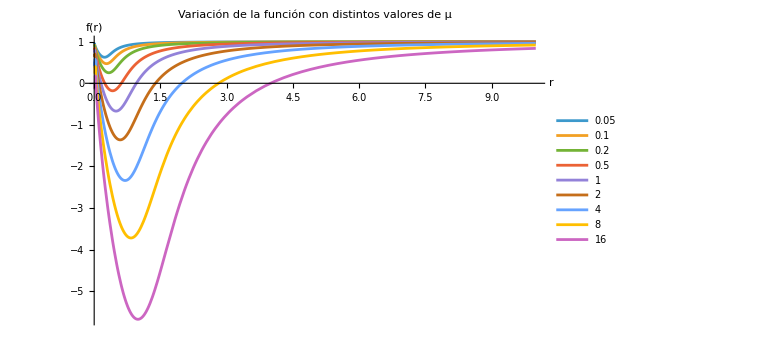

```mathematica
α:=0.03
b:=1
f3rees
Plot[Evaluate@Table[f3rees,{μ2,{0.05,0.1,0.2,0.5,1,2,4,8,16}}],{r2,0,10},PlotRange->All,MaxRecursion->6,PlotLegends->Placed[{"0.05","0.1","0.2","0.5","1","2","4","8","16"},Right],PlotLabel->"Variación de la función con distintos valores de μ",AxesLabel->{Style["r",18,Bold],Style["f(r)",18,Bold],Style["f(r)",18,Bold]},LabelStyle->Directive[15],TicksStyle->Directive[14],ImageSize->Large]
Clear[α,b]
```

#### α=0.005 y b=2

Power::infy: Infinite expression 1/0.^(1/3) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

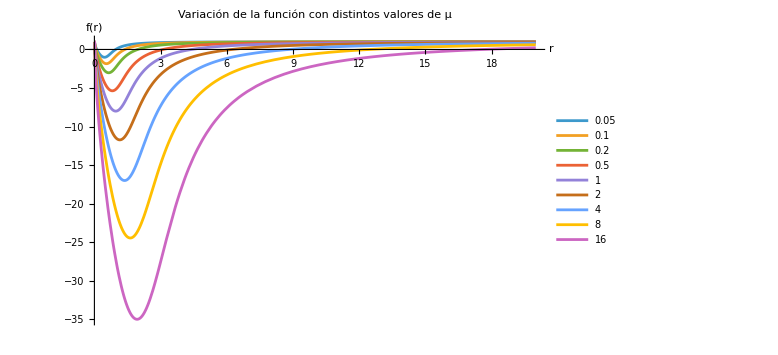

```mathematica
α:=0.005
b:=2
Plot[Evaluate@Table[f3rees,{μ,{0.05,0.1,0.2,0.5,1,2,4,8,16}}],{r2,0,20},PlotRange->All,MaxRecursion->6,PlotLegends->Placed[{"0.05","0.1","0.2","0.5","1","2","4","8","16"},Right],PlotLabel->"Variación de la función con distintos valores de μ",AxesLabel->{Style["r",18,Bold],Style["f(r)",18,Bold],Style["f(r)",18,Bold]},LabelStyle->Directive[15],TicksStyle->Directive[14],ImageSize->Large]
Clear[α,b]
```

#### α=0.005 y b=4

Power::infy: Infinite expression 1/0.^(1/3) encountered.

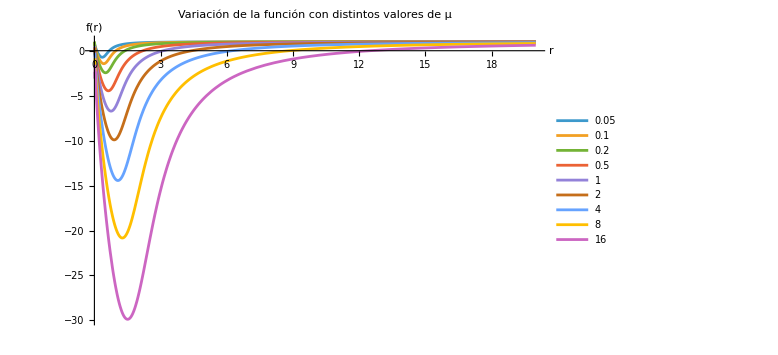

```mathematica
α:=0.005
b:=4
Plot[Evaluate@Table[f3rees,{μ,{0.05,0.1,0.2,0.5,1,2,4,8,16}}],{r2,0,20},PlotRange->All,MaxRecursion->6,PlotLegends->Placed[{"0.05","0.1","0.2","0.5","1","2","4","8","16"},Right],PlotLabel->"Variación de la función con distintos valores de μ",AxesLabel->{Style["r",18,Bold],Style["f(r)",18,Bold],Style["f(r)",18,Bold]},LabelStyle->Directive[15],TicksStyle->Directive[14],ImageSize->Large]
Clear[α,b]
```

#### α=0.005 y b=16

Power::infy: Infinite expression 1/0.^(1/3) encountered.

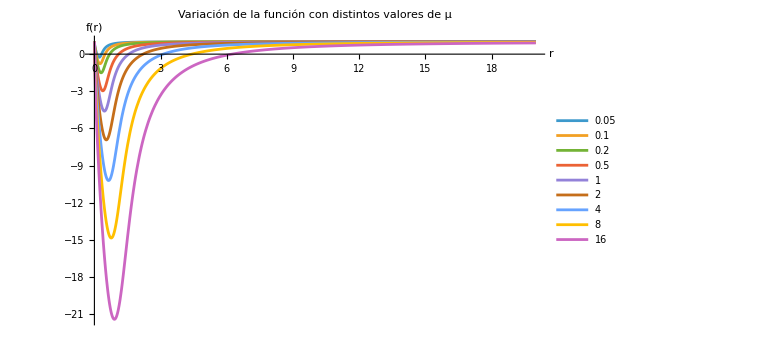

```mathematica
α:=0.005
b:=16
Plot[Evaluate@Table[f3rees,{μ,{0.05,0.1,0.2,0.5,1,2,4,8,16}}],{r2,0,20},PlotRange->All,MaxRecursion->6,PlotLegends->Placed[{"0.05","0.1","0.2","0.5","1","2","4","8","16"},Right],PlotLabel->"Variación de la función con distintos valores de μ",AxesLabel->{Style["r",18,Bold],Style["f(r)",18,Bold],Style["f(r)",18,Bold]},LabelStyle->Directive[15],TicksStyle->Directive[14],ImageSize->Large]
Clear[α,b]
```

#### α=0.01 y b=8/108

Power::infy: Infinite expression 1/0.^(1/3) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

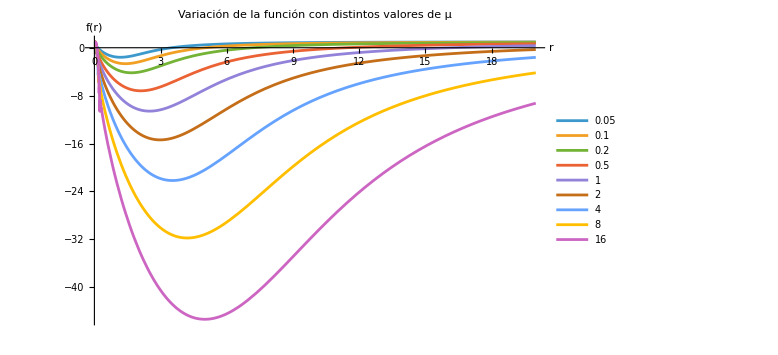

```mathematica
α:=0.01
b:=8/108
Plot[Evaluate@Table[f3rees,{μ,{0.05,0.1,0.2,0.5,1,2,4,8,16}}],{r2,0,20},PlotRange->All,MaxRecursion->6,PlotLegends->Placed[{"0.05","0.1","0.2","0.5","1","2","4","8","16"},Right],PlotLabel->"Variación de la función con distintos valores de μ",AxesLabel->{Style["r",18,Bold],Style["f(r)",18,Bold],Style["f(r)",18,Bold]},LabelStyle->Directive[15],TicksStyle->Directive[14],ImageSize->Large]
Clear[α,b]
```

### Invariante de Kretschman

```mathematica
NN[r2_]:=1
b:=1
α:=1
f[r2_]:=f3rees
Krt[r2_]=Assuming[r2>0&&μ>0&&α>0&&b>0,Simplify[1/(r2^4 NN[r2]^2)(9 r2^4 f'[r2]^2 NN'[r2]^2+6 r2^4 NN[r2] f'[r2] NN'[r2] f''[r2]+NN[r2]^2 (12-24 f[r2]+12 f[r2]^2+6 r2^2 f'[r2]^2+r^4 f''[r2]^2)+12 r2^4 f[r2] f'[r2] NN'[r2] NN''[r2]+4 f[r2] NN[r] (3 r2^2 f'[r2] NN'[r2]+r2^4 f''[r2] NN''[r2])+4 f[r2]^2 (3 r2^2 NN'[r2]^2+r2^4 NN''[r2]^2))]]
```

(12 (-1+f3rees)^2)/r2^4